```mathematica
ClearAll["Global`*"]
```

```mathematica
M//N
```

0.000013

```mathematica
M:=130/10^7 
p:=1.00
ϕini:=5.45315
ϕend:=0.940178
h1:=0.05
V0[p_]:=6((2p-1)/(4 p))M^2(1/(2 p))^(1/(2 p-1))
h[ϕ_]:=-1/(M (-2+3 p))3 2^((2-3 p)/(-1+2 p)) p^((1-p)/(-1+2 p)) (-1+2 p)^(3/2)  ((-1+ⅇ^(√(2/3) ϕ))^((2-3 p)/(1-2 p)) Hypergeometric2F1[1,(2-3 p)/(1-2 p),(3-5 p)/(1-2 p),((-1+ⅇ^(√(2/3) ϕ)) (-1+p))/p]-(-1+ⅇ^(√(2/3) ϕini))^((2-3 p)/(1-2 p)) Hypergeometric2F1[1,(2-3 p)/(1-2 p),(3-5 p)/(1-2 p),((-1+ⅇ^(√(2/3) ϕini)) (-1+p))/p])
```

```mathematica
root[t_]:=FindRoot[h[ϕ]-t==0,{ϕ,ϕini}]
```

```mathematica
ϕsr[t_]:=(ϕ/.First[root[t]])
```

```mathematica
ϕsrp[t_]:=(ϕsr[t+h1]-ϕsr[t-h1])/(2h1)
```

```mathematica
w=NDSolve[{ϕt''[t]+3Sqrt[1/3((ϕt'[t])^2/2+ⅇ^(-2 √(2/3) ϕt[t]) (-1+ⅇ^(√(2/3) ϕt[t]))^((2 p)/(-1+2 p)) V0[p])] ϕt'[t] -2 √(2/3) ⅇ^(-2 √(2/3) ϕt[t]) (-1+ⅇ^(√(2/3) ϕt[t]))^((2 p)/(-1+2 p)) V0[p]+(2 √(2/3) ⅇ^(-√(2/3) ϕt[t]) (-1+ⅇ^(√(2/3) ϕt[t]))^(-1+(2 p)/(-1+2 p)) p V0[p])/(-1+2 p)==0,ϕt[0]==ϕsr[0],ϕt'[0]==ϕsrp[0]},{ϕt,ϕt',ϕt'',ϕt'''},{t,-280000,1.10 10^7}, MaxSteps->1000000,StartingStepSize->0.0001,MaxStepSize->200]
```

{{ϕt→                                        7
InterpolatingFunction[{{-280000., 1.1 10 }}, <>],ϕt'→                                        7
InterpolatingFunction[{{-280000., 1.1 10 }}, <>],ϕt''→                                        7
InterpolatingFunction[{{-280000., 1.1 10 }}, <>],ϕt^(3)→                                        7
InterpolatingFunction[{{-280000., 1.1 10 }}, <>]}}

```mathematica
w[[1,1,2]]
```

7
InterpolatingFunction[{{-280000., 1.1 10 }}, <>]

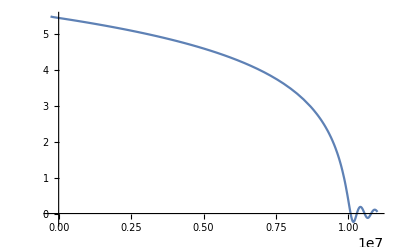

```mathematica
Plot[%14[x],{x,-280000.,1.1*^7}]
```

```mathematica
Plot[%38[x],{x,-280000,1.1*^7}]
```

-Graphics-

```mathematica
ϕ[t_]:=(ϕt/.First[w])[t];
pϕ[t_]:=(ϕt'/.First[w])[t];
ppϕ[t_]:=(ϕt''/.First[w])[t];
pppϕ[t_]:=(ϕt'''/.First[w])[t];
```

```mathematica
ϕ[t]
```

7
InterpolatingFunction[{{-280000., 1.1 10 }}, <>][t]

```mathematica
M:=130/10^7 
p:=1.00
ϕini:=5.45315
ϕend:=0.940178
h1:=0.05
V0[p_]:=6((2p-1)/(4 p))M^2(1/(2 p))^(1/(2 p-1))
h[ϕ_]:=-1/(M (-2+3 p))3 2^((2-3 p)/(-1+2 p)) p^((1-p)/(-1+2 p)) (-1+2 p)^(3/2)  ((-1+ⅇ^(√(2/3) ϕ))^((2-3 p)/(1-2 p)) Hypergeometric2F1[1,(2-3 p)/(1-2 p),(3-5 p)/(1-2 p),((-1+ⅇ^(√(2/3) ϕ)) (-1+p))/p]-(-1+ⅇ^(√(2/3) ϕini))^((2-3 p)/(1-2 p)) Hypergeometric2F1[1,(2-3 p)/(1-2 p),(3-5 p)/(1-2 p),((-1+ⅇ^(√(2/3) ϕini)) (-1+p))/p])
root[t_]:=FindRoot[h[ϕ]-t==0,{ϕ,ϕini}]
ϕsr[t_]:=(ϕ/.First[root[t]])
ϕsrp[t_]:=(ϕsr[t+h1]-ϕsr[t])/h1
w=NDSolve[{ϕt''[t]+3Sqrt[1/3((ϕt'[t])^2/2+ⅇ^(-2 √(2/3) ϕt[t]) (-1+ⅇ^(√(2/3) ϕt[t]))^((2 p)/(-1+2 p)) V0[p])] ϕt'[t] -2 √(2/3) ⅇ^(-2 √(2/3) ϕt[t]) (-1+ⅇ^(√(2/3) ϕt[t]))^((2 p)/(-1+2 p)) V0[p]+(2 √(2/3) ⅇ^(-√(2/3) ϕt[t]) (-1+ⅇ^(√(2/3) ϕt[t]))^(-1+(2 p)/(-1+2 p)) p V0[p])/(-1+2 p)==0,ϕt[0]==ϕsr[0],ϕt'[0]==ϕsrp[0]},{ϕt,ϕt',ϕt'',ϕt'''},{t,-280000,1.10 10^7}, MaxSteps->1000000,StartingStepSize->0.0001,MaxStepSize->200];
ϕ[t_]:=(ϕt/.First[w])[t];
pϕ[t_]:=(ϕt'/.First[w])[t];
ppϕ[t_]:=(ϕt''/.First[w])[t];
pppϕ[t_]:=(ϕt'''/.First[w])[t];
ww=NDSolve[{at'[t]/at[t]==Sqrt[1/3((ϕ'[t])^2/2+ⅇ^(-2 √(2/3) ϕ[t]) (-1+ⅇ^(√(2/3) ϕ[t]))^((2 p)/(-1+2 p)) V0[p])],at[0]==1.},{at,at',at'',at'''},{t,-280000,1.10 10^7},MaxSteps->1000000,StartingStepSize->0.0001,MaxStepSize->200];
a[t_]:=(at/.First[ww])[t];
pa[t_]:=(at'/.First[ww])[t];
ppa[t_]:=(at''/.First[ww])[t];
pppa[t_]:=(at'''/.First[ww])[t];
H[t_]:=pa[t]/a[t]
z[t_]:=(a[t]pϕ[t])/H[t]
tend=t/.FindRoot[ϕ[t]==ϕend,{t,9.8 10^6}]; 
Efolds=Log[a[tend]/a[0]];
pH[t_]=D[H[t],t];
z[t_]:=((a[t])^2 pϕ[t])/pa[t];
pz[t_]:=a[t] (pϕ[t] (2-(a[t] ppa[t])/pa[t]^2)+(a[t] ppϕ[t])/pa[t])
ppz[t_]:=2 pa[t] pϕ[t]+(2 a[t]^2 pϕ[t] ppa[t]^2)/pa[t]^3+4 a[t] ppϕ[t]-(a[t]^2 (2 ppa[t] ppϕ[t]+pϕ[t] pppa[t]))/pa[t]^2+(a[t] (-2 pϕ[t] ppa[t]+a[t] pppϕ[t]))/pa[t]
```

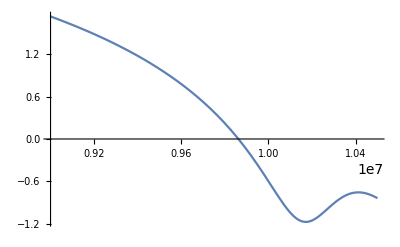

```mathematica
Plot[ϕ[t]-ϕend,{t,0.9 10^7,1.05 10^7},PlotRange->All]
```

```mathematica
tend
```

9.86197×10^6

```mathematica
conformal=NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'},{t,0,9.7 10^6},AccuracyGoal->10,PrecisionGoal->10,WorkingPrecision->15,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:=(conf/.First[conformal])[t];
pη[t_]:=(conf'/.First[conformal])[t];
rhsScalar[k_,t_]:=1/(a[t])^2(k^2-a[t]/z[t]((pa[t]pz[t])+(a[t]ppz[t])));
rhsTensor[k_,t_]:=((k/a[t])^2-(pa[t]/a[t])^2-ppa[t]/a[t]);
hc[k_]:=Rationalize[FindRoot[k-pa[t],{t,9.7 10^6}][[1,2]],0];
uini[k_,t_]:=Rationalize[Exp[-I k η[t]]/Sqrt[2k],0];
diffuini[k_,t_]:=Rationalize[-Exp[-I k η[t]]/Sqrt[2k](I k pη[t]),0];
nzeros[k_]:=n/.First[NSolve[n==Pi^-1 k(η[hc[k]]-η[0]),n,WorkingPrecision->15]]
etabuch[k_]:=NSolve[k (η[hc[k]]-eta)==500Pi,eta]
etaini[k_]:=NSolve[k (η[hc[k]]-eta)==300Pi,eta]
suptbuch[k_]:=FindRoot[η[t]==(eta/.First[etabuch[k]]),{t,500}][[1,2]]
suptini[k_]:=FindRoot[η[t]==(eta/.First[etaini[k]]),{t,500}][[1,2]]
tbuch[k_]:=Piecewise[{{hc[k]*0.001,k≤.06},{suptbuch[k],k>.06}}];
tini[k_]:=Piecewise[{{hc[k]*.05,k≤.06},{suptini[k],k>.06}}];
(*kcomoving[kphy_]:=kphy*100*(2.99792458*^5)/(Sqrt[8Pi]67.4)*)
```

```mathematica
prere[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,StartingStepSize->.0001,MaxStepSize->10,InterpolationOrder->All];
re[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsScalar[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,StartingStepSize->.001,MaxStepSize->10,InterpolationOrder->All];
preim[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,StartingStepSize->.0001,MaxStepSize->10,InterpolationOrder->All];
im[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsScalar[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,StartingStepSize->.001,MaxStepSize->10,InterpolationOrder->All];
x[k_]:=u/.First[re[k]]
y[k_]:=v/.First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l2''[t]+l2'[t]H[t]+l2[t](k/a[t])^2==0,l2[tbuch[k]]==Re[uini[k,tbuch[k]]],l2'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l2,l2'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,StartingStepSize->.0001,MaxStepSize->10,InterpolationOrder->All];
re2[k_]:=NDSolve[{u2''[t]+u2'[t]H[t]+u2[t]rhsTensor[k,t]==0,u2[tini[k]]==Rationalize[(l2/.First[prere2[k]])[tini[k]],0],u2'[tini[k]]==Rationalize[(l2'/.First[prere2[k]])[tini[k]],0]},u2,{t,tini[k],3 hc[k]},MaxSteps->Infinity,StartingStepSize->.001,MaxStepSize->10,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g2''[t]+g2'[t]H[t]+g2[t](k/a[t])^2==0,g2[tbuch[k]]==Im[uini[k,tbuch[k]]],g2'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g2,g2'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,StartingStepSize->.0001,MaxStepSize->10,InterpolationOrder->All];
im2[k_]:=NDSolve[{v2''[t]+v2'[t]H[t]+v2[t]rhsTensor[k,t]==0,v2[tini[k]]==Rationalize[(g2/.First[preim2[k]])[tini[k]],0],v2'[tini[k]]==Rationalize[(g2'/.First[preim2[k]])[tini[k]],0]},v2,{t,tini[k],3 hc[k]},MaxSteps->Infinity,StartingStepSize->.001,MaxStepSize->10,InterpolationOrder->All];
x2[k_]:=u2/.First[re2[k]]
y2[k_]:=v2/.First[im2[k]]
```

```mathematica
PS[k_]:=k^3/(2 Pi^2(z[3 hc[k]])^2)Abs[(x[k])[3 hc[k]]+I (y[k])[3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]
```

```mathematica
(*cmb*)
```

```mathematica
k:=0.05
h2:=0.05
PS[k]
```

2.14893×10^-9

```mathematica
k:=0.002
PT[k]
```

1.04292×10^-12

```mathematica
(*Paper*)
LogPSpi=Log[10^(10)2.1489278249014394*^-9]
```

3.06755

```mathematica
(*File*)
premarcas1=Table[10^i,{i,1/10,1,1/10}];
marcas1={.0001};
Do[AppendTo[marcas1,Table[N[premarcas1[[i]]/10^(10-j)],{i,1,Length[premarcas1]}]],{j,6,10}];
marcas1=Flatten[marcas1]
```

{0.0001,0.000125893,0.000158489,0.000199526,0.000251189,0.000316228,0.000398107,0.000501187,0.000630957,0.000794328,0.001,0.00125893,0.00158489,0.00199526,0.00251189,0.00316228,0.00398107,0.00501187,0.00630957,0.00794328,0.01,0.0125893,0.0158489,0.0199526,0.0251189,0.0316228,0.0398107,0.0501187,0.0630957,0.0794328,0.1,0.125893,0.158489,0.199526,0.251189,0.316228,0.398107,0.501187,0.630957,0.794328,1.,1.25893,1.58489,1.99526,2.51189,3.16228,3.98107,5.01187,6.30957,7.94328,10.}

```mathematica
strm=OpenWrite["/Users/crojas/Documents/Research/inflation/gStarobinsky/phase-integral/graph/PTnum_p=1.000.dat",FormatType->OutputForm];
For[i=0,i<Length[marcas1],Write[strm,k=marcas1[[i]],"   ",CForm[PT[k]]],i++]
Close[strm];
```

```mathematica
(*strm=OpenWrite["/Users/crojas/Documents/Research/inflation/gStarobinsky/phase-integral/graph/PTnum_p=1.000.dat",FormatType->OutputForm];
For[i=10,i<1000000,i=i+1000,Write[strm,k=N[i/100000],"    ",CForm[PT[k]]]]
Close[strm];*)
```

$Aborted

```mathematica
(*Print*)
premarcas1=Table[10^i,{i,1/10,1,1/10}];
marcas1={.0001};
Do[AppendTo[marcas1,Table[N[premarcas1[[i]]/10^(10-j)],{i,1,Length[premarcas1]}]],{j,6,10}];
marcas1=Flatten[marcas1]
```

{0.0001,0.000125893,0.000158489,0.000199526,0.000251189,0.000316228,0.000398107,0.000501187,0.000630957,0.000794328,0.001,0.00125893,0.00158489,0.00199526,0.00251189,0.00316228,0.00398107,0.00501187,0.00630957,0.00794328,0.01,0.0125893,0.0158489,0.0199526,0.0251189,0.0316228,0.0398107,0.0501187,0.0630957,0.0794328,0.1,0.125893,0.158489,0.199526,0.251189,0.316228,0.398107,0.501187,0.630957,0.794328,1.,1.25893,1.58489,1.99526,2.51189,3.16228,3.98107,5.01187,6.30957,7.94328,10.}

```mathematica
powerspectra=Table[k=marcas1[[i]];{k,PS[k]},{i,1,Length[marcas1]}]
```

{{0.0001,2.66497×10^-9},{0.0000125893,2.81514×10^-9},{0.0000158489,3.16987×10^-9},{0.0000199526,3.20403×10^-9},{0.0000251189,2.88015×10^-9},{0.0000316228,2.64537×10^-9},{0.0000398107,2.79511×10^-9},{0.0000501187,2.73135×10^-9},{0.0000630957,2.72383×10^-9},{0.0000794328,2.66913×10^-9},{0.0001,2.66497×10^-9},{0.000125893,2.64446×10^-9},{0.000158489,2.62911×10^-9},{0.000199526,2.60921×10^-9},{0.000251189,2.58955×10^-9},{0.000316228,2.5725×10^-9},{0.000398107,2.55267×10^-9},{0.000501187,2.53219×10^-9},{0.000630957,2.51227×10^-9},{0.000794328,2.49311×10^-9},{0.001,2.47308×10^-9},{0.00125893,2.45331×10^-9},{0.00158489,2.43421×10^-9},{0.00199526,2.41502×10^-9},{0.00251189,2.39553×10^-9},{0.00316228,2.3765×10^-9},{0.00398107,2.35746×10^-9},{0.00501187,2.33848×10^-9},{0.00630957,2.31958×10^-9},{0.00794328,2.30039×10^-9},{0.01,2.2815×10^-9},{0.0125893,2.26246×10^-9},{0.0158489,2.24334×10^-9},{0.0199526,2.22405×10^-9},{0.0251189,2.20497×10^-9},{0.0316228,2.18572×10^-9},{0.0398107,2.16692×10^-9},{0.0501187,2.14833×10^-9},{0.0630957,2.13411×10^-9},{0.0794328,2.11606×10^-9},{0.1,2.09788×10^-9},{0.125893,2.08026×10^-9},{0.158489,2.06229×10^-9},{0.199526,2.04446×10^-9},{0.251189,2.0267×10^-9},{0.316228,2.00908×10^-9},{0.398107,1.99154×10^-9},{0.501187,1.97431×10^-9},{0.630957,1.95679×10^-9},{0.794328,1.93922×10^-9},{1.,1.92195×10^-9},{1.25893,1.90468×10^-9},{1.58489,1.88779×10^-9},{1.99526,1.87071×10^-9},{2.51189,1.85369×10^-9},{3.16228,1.8367×10^-9},{3.98107,1.81992×10^-9},{5.01187,1.80335×10^-9},{6.30957,1.78653×10^-9},{7.94328,1.7702×10^-9},{10.,1.7533×10^-9}}

```mathematica
powerspectra:={{0.0001,2.6649699829335473*^-9},{0.00012589254117941674,2.6444648012276854*^-9},{0.00015848931924611134,2.629110577975933*^-9},{0.00019952623149688798,2.609206874634553*^-9},{0.000251188643150958,2.5895467883359057*^-9},{0.00031622776601683794,2.5725049198070195*^-9},{0.0003981071705534972,2.5526738137051486*^-9},{0.0005011872336272722,2.532194617956265*^-9},{0.0006309573444801933,2.512266708018019*^-9},{0.0007943282347242815,2.493109948542392*^-9},{0.001,2.4730831332549487*^-9},{0.0012589254117941673,2.4533093347945276*^-9},{0.0015848931924611134,2.4342142271227003*^-9},{0.00199526231496888,2.41502306393191*^-9},{0.0025118864315095803,2.3955306427396067*^-9},{0.0031622776601683794,2.3765022451991303*^-9},{0.003981071705534972,2.3574610829319757*^-9},{0.005011872336272723,2.3384800623623474*^-9},{0.006309573444801933,2.3195778364684225*^-9},{0.007943282347242816,2.3003906762374067*^-9},{0.01,2.281501558757094*^-9},{0.012589254117941673,2.262464785956547*^-9},{0.015848931924611134,2.2433386747961304*^-9},{0.0199526231496888,2.2240477529826095*^-9},{0.0251188643150958,2.2049693178215594*^-9},{0.0316227766016838,2.185722016105354*^-9},{0.03981071705534972,2.1669205288371366*^-9},{0.05011872336272723,2.1483346970276237*^-9},{0.06309573444801933,2.1341129841305365*^-9},{0.07943282347242815,2.116062320409307*^-9},{0.1,2.097882941957296*^-9},{0.12589254117941673,2.0802627127139997*^-9},{0.15848931924611134,2.0622851571957873*^-9},{0.19952623149688797,2.044457489236526*^-9},{0.251188643150958,2.0267010060275054*^-9},{0.31622776601683794,2.0090787871354417*^-9},{0.3981071705534972,1.991537226448268*^-9},{0.5011872336272722,1.9743098389777*^-9},{0.6309573444801932,1.9567946053993264*^-9},{0.7943282347242815,1.9392182541575646*^-9},{1.,1.9219513341416064*^-9},{1.2589254117941673,1.9046786539534143*^-9},{1.5848931924611136,1.88778881399842*^-9},{1.9952623149688795,1.870707276383558*^-9},{2.51188643150958,1.8536863302206002*^-9},{3.1622776601683795,1.8366961186135501*^-9},{3.9810717055349722,1.8199187726745867*^-9},{5.011872336272722,1.8033534878678913*^-9},{6.309573444801933,1.7865273547004179*^-9},{7.943282347242816,1.7702032961060402*^-9},{10.,1.7533033985065645*^-9}}
```

```mathematica
Clear[k]
```

```mathematica
fit=NonlinearModelFit[powerspectra,cons  k^(spec-1),{spec,cons},k]
```

FittedModel[(1.92366×10^-9)/k^0.036232]

```mathematica
Clear[k]
```

```mathematica
PPS[k_]:=(1.9236568800579665*^-9)/k^0.036231954708477176
dPPS[k_]=D[PPS[k],{k,1}];
nnS[k_]=1+k/PPS[k]dPPS[k];
```

```mathematica
k:=0.05
h:=0.001
PPS[k]
nnS[k]
```

2.14421×10^-9

0.963768

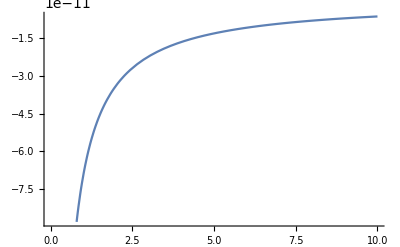

```mathematica
Plot[dPPS[k],{k,0,10},PlotStyle->All]
```

```mathematica
(**************************************)
```

```mathematica
ps:=Interpolation[powerspectra]
dps=D[ps[k],k];
```

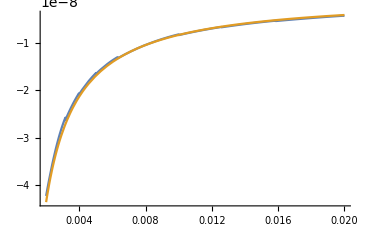

```mathematica
Plot[{dps,dpps[k]},{k,0.002,0.02},PlotRange->All]
```

```mathematica
fit=NonlinearModelFit[powerspectra,cons  x^(spec-1),{spec,cons},x]
```

FittedModel[(1.92366×10^-9)/x^0.036232]

```mathematica
fit["BestFitParameters"]
```

{spec→0.963768,cons→1.92366×10^-9}

```mathematica
k:=0.05
ns=1+k/ps[k]dps
```

0.964792